```mathematica
f0=0.1234
```

0.1234

```mathematica
f0x=0.9876
```

0.9876

```mathematica
f1=0.5678
```

0.5678

```mathematica
f1x=-0.1111
```

-0.1111

```mathematica
c0=f0
```

0.1234

```mathematica
c1=3*c0+f0x
```

1.3578

```mathematica
c3=f1
```

0.5678

```mathematica
c2=3*c3-f1x
```

1.8145

```mathematica
g=c0*(1-x)^3+c1*x*(1-x)^2+c2*x^2*(1-x)+c3*x^3
```

0.1234 (1-x)^3+1.3578 (1-x)^2 x+1.8145 (1-x) x^2+0.5678 x^3

```mathematica
gx=D[g,x]
```

0.9876 (1-x)^2+0.9134 (1-x) x-0.1111 x^2

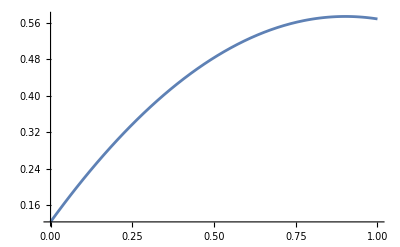

```mathematica
Plot[g,{x,0,1}]
```

```mathematica
points=Import["C:\\Users\\deber\\GeometricTools\\GTL\\UnitTests\\Mathematics\\Interpolation\\1D\\HermiteCubic1Order0Single.txt","CSV"];
```

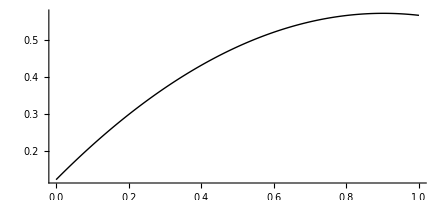

```mathematica
Graphics[Line[points],Axes->True,AspectRatio->Full]
```

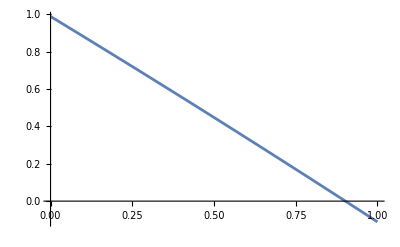

```mathematica
Plot[gx,{x,0,1}]
```

```mathematica
points=Import["C:\\Users\\deber\\GeometricTools\\GTL\\UnitTests\\Mathematics\\Interpolation\\1D\\HermiteCubic1OrderXSingle.txt","CSV"];
```

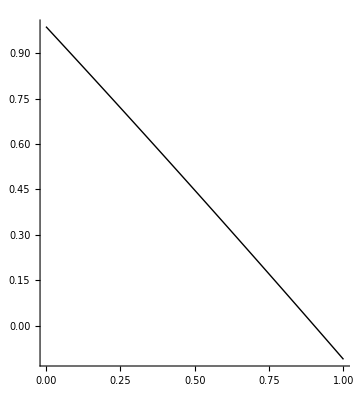

```mathematica
Graphics[Line[points],Axes->True,AspectRatio->Full]
```